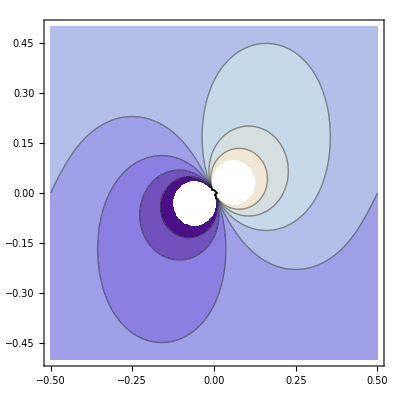

```mathematica
(* Cycle potential on a cylinder *)
ContourPlot[Re[(1+I/2)π Cot[(x+I y)π]],{x,-1/2,1/2},{y,-1/2,1/2}]
```

```mathematica
(* Real expression *)
(I (Exp[2 I (x + I y)] + 1)/(Exp[2 I (x+I y)] - 1)-I (Exp[-2 I (x - I y)] + 1)/(Exp[-2 I (x-I y)] - 1))/2//FullSimplify
```

-Sin[2 x]/(Cos[2 x]-Cosh[2 y])

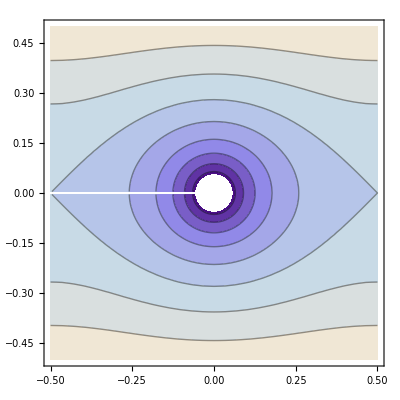

```mathematica
(* Cycle monopole on cylinder *)
ContourPlot[Re[π Log[Sin[(x+I y)π]]],{x,-1/2,1/2},{y,-1/2,1/2}]
```

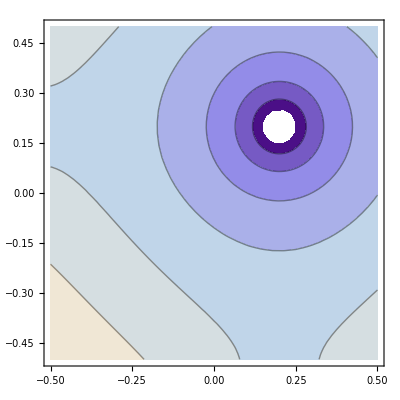

```mathematica
(* monopole cycle potential on a torus *)
ContourPlot[Re[Log[WeierstrassSigma[x+I y-1/5-1/5I,WeierstrassInvariants[{1/2,I/2}]]]],{x,-1/2,1/2},{y,-1/2,1/2}]
```

```mathematica
{a,b}=WeierstrassInvariants[{1/2,I/2}]//N;
W[x_,y_]:=WeierstrassP[x+I y,{a,b}]
WP[x_,y_]:=WeierstrassPPrime[x+I y,{a,b}]
WPP[x_,y_]:=-a/2+6WeierstrassP[x+I y,{a,b}]^2
Deriv[x_,y_]:=(WPP[x,y] W[x,y]-(WP[x,y])^2)/W[x,y]^2
```

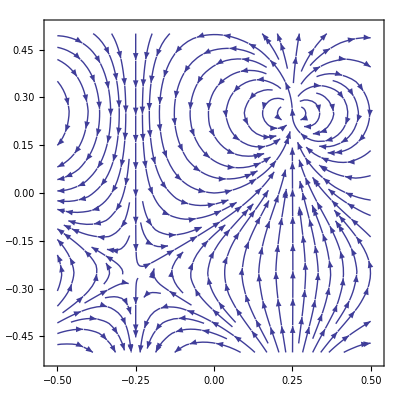

```mathematica
StreamPlot[{Re[I W[x-1/4,y-1/4]],Re[-W[x-1/4,y-1/4]]},{x,-1/2,1/2},{y,-1/2,1/2}]
```

```mathematica
yourFunc=Function[{u,v},Re[WeierstrassZeta[u+I v,{a,b}]]];

ParametricPlot3D[{(2+Cos[2 π v]) Sin[2 π u],(2+Cos[2 π v]) Cos[2 π u],Sin[2 π v]},{u,0,1},{v,0,1},MeshFunctions->Function[{x,y,z,u,v},yourFunc[u,v]],Mesh->{Table[i,{i,-100,100,5}]},MeshStyle->Directive[Blue,Thick],PlotPoints->50]
```

-Graphics3D-

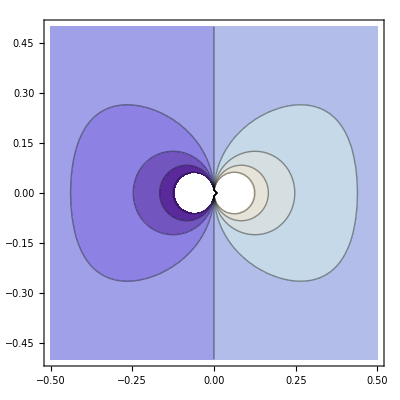

```mathematica
ContourPlot[Re[WeierstrassZeta[x + I y,{a,b}]],{x,-1/2,1/2},{y,-1/2,1/2}]
```

```mathematica
(*Sphere*)
yourFunc=Function[{u,v},Cos[u]/Sin[v]-Cos[u]Cot[v]];

ParametricPlot3D[{Cos[v]Sin[u],Sin[v]Sin[u],Cos[u]},{u,0,2π},{v,0,2π},MeshFunctions->Function[{x,y,z,u,v},yourFunc[u,v]],Mesh->{Table[i,{i,-100,100,5}]},MeshStyle->Directive[Blue,Thick],PlotPoints->50]
```

-Graphics3D-

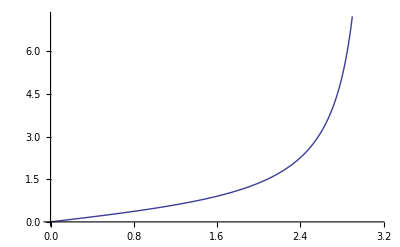

```mathematica
Plot[(Cos[u]/Sin[v]-Cos[u]Cot[v])/.u->1/2,{v,0,π}]
```

```mathematica
Integrate[WeierstrassZeta[z,{a,b}],z]
```

Log[WeierstrassSigma[z,{a,b}]]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

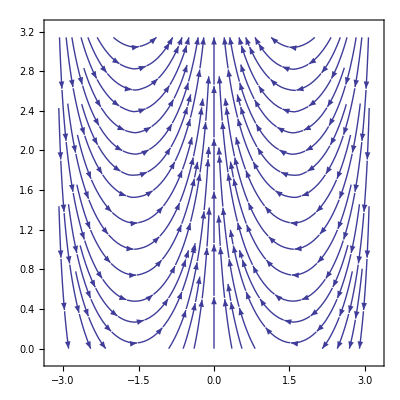
-Graphics--Graphics3D-

```mathematica
sp=StreamPlot[{-Sin[ϕ] Tan[θ/2]/Sin[θ],1/2Cos[ϕ](1+ Tan[θ/2]^2)},{ϕ,-π,π},{θ,0,π},ImageSize->400];

sp3d=Graphics3D[sp[[1]]/.Arrow[z_]:>Arrow[z/.{x_Real,y_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],ImageSize->400];
Row[{sp,sp3d},Spacer[5]]
```

```mathematica
ComplexExpand[Im[(1-z)^2/(x + I y)^2]]/.{x->Sin[θ]Cos[ϕ],y->Sin[θ]Sin[ϕ],z->Cos[θ]}//Simplify
```

-2 Cos[ϕ] Sin[ϕ] Tan[θ/2]^2

```mathematica
ComplexExpand[Re[(1-z)^2/(x+ⅈ y)^2]]/.{x->Sin[θ]Cos[ϕ],y->Sin[θ]Sin[ϕ],z->Cos[θ]}//Simplify
```

Cos[2 ϕ] Tan[θ/2]^2

```mathematica
ComplexExpand[(1-z)/(x+ⅈ y)]/.{x->Sin[θ]Cos[ϕ],y->Sin[θ]Sin[ϕ],z->Cos[θ]}//Simplify
```

(Cos[ϕ]-ⅈ Sin[ϕ]) Tan[θ/2]

```mathematica
Cos[ϕ] Tan[θ/2]== Cos[ϕ]/Sin[θ](1-Cos[θ])//Simplify
```

True